```mathematica
folder="C:\\Users\\jacks\\Documents\\GitHub\\cdt_rust\\data\\Analytic_Volume_10_TimeSize_5";files=FileNames["*.csv",folder];
analyticData=Flatten[Import[#]&/@files,1];
```

```mathematica
file="C:\\Users\\jacks\\Documents\\GitHub\\cdt_rust\\data\\Statistical_Volume_10_TimeSize_5.csv";
statisticalData=Import[file];
```

```mathematica
statCounts = Counts[statisticalData[[;;,1]]]/Length[statisticalData];
analCounts = Counts[analyticData[[;;,1]]]/Length[analyticData];
```

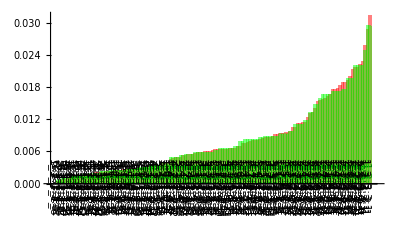

```mathematica
Show[BarChart[Sort[statCounts],ChartLabels->Placed[Automatic,Below,Rotate[#,-Pi/2]&],ChartStyle->Directive[Red,Opacity[0.5]]],
BarChart[Sort[analCounts],ChartLabels->Placed[Automatic,Below,Rotate[#,-Pi/2]&],ChartStyle->Directive[Green,Opacity[0.5]]]]
```

```mathematica
residual = AssociationThread[Keys[analCounts],MapThread[Subtract,{Values[analCounts],Values[statCounts]}]];
```

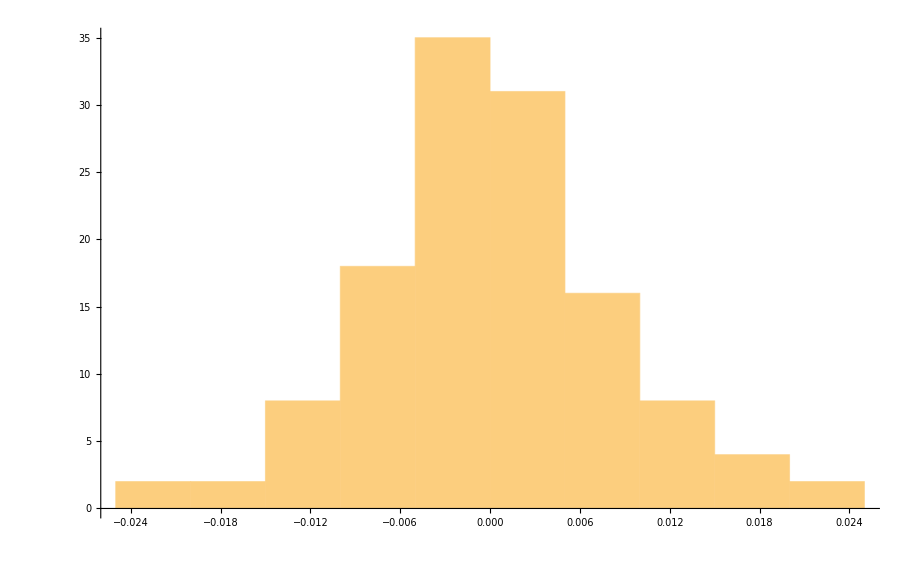

```mathematica
Histogram[residual,10]
```

```mathematica
pValue=KolmogorovSmirnovTest[Values[analCounts],Values[statCounts]]
```

0.986408